# The Bell Inequalities

Alice and Bob both possess an instrument S(θ,ϕ) that  measures the spin along an axis defined by the unit vector 

-Graphics-

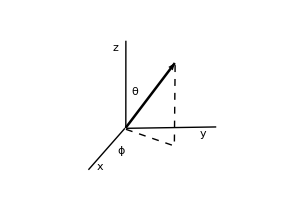

```mathematica
S[θ_,ϕ_]={{Cos[θ],Exp[-I ϕ]Sin[θ]},{Exp[I ϕ]Sin[θ],-Cos[θ]}};
(* up[θ,ϕ] represents qubit state aligned along direction n⃗ *)
up[θ_,ϕ_]={Cos[θ/2],Exp[I ϕ] Sin[θ/2]};
down[θ_,ϕ_]={-Sin[θ/2],ⅇ^(ⅈ ϕ) Cos[θ/2]};
(* down[θ,ϕ] represents qubit state aligned along direction OverVector[-n] *)
unit={{1,0},{0,1}};
```

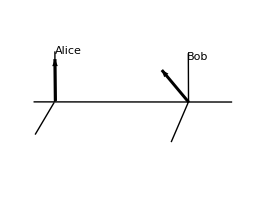
For their measurements, Alice and Bob choose three possible angles A, B, C, so that S⃗·n⃗ is aligned in the x-z plane. They let θ=θ_A, ϕ_A=0,   θ=θ_B, ϕ_B=0,  θ=θ_C   ϕ_B=π  (i.e. A and B are in the first and second quadrant of the z-x plane, and C is in the 4'th quadrant, going around counterclockwise in that plane.)

Alice and Bob measure the spin of the qubits they each receive. The pair of qubits are in the Bell state

-Graphics-

If Alice chooses instrument A and Bob instrument B, their measurement setup would look  like 

-Graphics-

After a repeated number of measurements we calculate the expectation value (correlation) of the product A B for those measurements. According to the Born rule, it is given by the expression  ⟨ψ| A B |ψ⟩   which we evaluate below.

```mathematica
(* psi is the Bell state *)
psi=1/Sqrt[2](Flatten[KroneckerProduct[{1,0},{0,1}]]-Flatten[KroneckerProduct[{0,1},{1,0}]]);
MatrixForm[psi]
```

(0
1/(√2)
-1/(√2)
0)

```mathematica
(* measurement devices for Alice and Bob respectively *)
A=KroneckerProduct[S[θA,0],unit];
B=KroneckerProduct[unit,S[θB,0]];
```

```mathematica
(* correlation expectation for measurements A, B *)
EAB=FullSimplify[Conjugate[psi].A.B.psi]
```

-Cos[θA-θB]

So if A and B have the same orientation, we find that  EAB = -1.  That is perfect anti-correlation, similar to a Bertlemann's socks scenario. Consider the case where Alice has orientation A and Bob orientation C

```mathematica
c=KroneckerProduct[unit,S[θC,Pi]];
EAC=FullSimplify[Conjugate[psi].A.c.psi]
```

-Cos[θA+θC]

Finally we choose Alice to have orientation B and Bob orientation C, then

```mathematica
B=KroneckerProduct[S[θB,0],unit];
EBC=FullSimplify[Conjugate[psi].B.c.psi]
```

-Cos[θB+θC]

### Bell's proof

John Bell asked the question, what would the correlation values be if we strictly enforced local realism? Under this restriction the random variable A=±1 obtained with measurements of Alice's device must only depend on the orientation of Alice's device  A = A((n̂)_A) , it should not depend on (n̂)_B the orientation of Bob's device. However it may depend on other local variables, which we collectively call λ, and are hidden from us. These hidden parameters determine the properties of both Alice's and Bob's observed particles . Therefore we let  A = A((n̂)_A,λ). In the same manner, for the random variable measured by Bob, we assume B = B((n̂)_B,λ).   So the expectation value  

⟨A B⟩  =  ∫ⅆλ ρ(λ) A((n̂)_A,λ) B((n̂)_B,λ) 

is the central assumption of Bell's local realism requirement. Here ρ(λ) is a probability for the system to be in a state for a given value of λ, the hidden variables.  Now if ρ(λ) is a probability distribution

 ∫ⅆλ ρ(λ)=1

If  (n̂)_A=(n̂)_B  we find perfect anti-correlation, i.e. ⟨A B⟩  = -1, therefore we require B((n̂)_B,λ) = -A((n̂)_A,λ) since 

- ∫ⅆλ ρ(λ) A((n̂)_A,λ) A((n̂)_B,λ)  = -1  if (n̂)_B=(n̂)_A   (as A^2=1).

and the former relation must hold for all possible orientations. Therefore,

⟨A B⟩  =  -∫ⅆλ ρ(λ) A((n̂)_A,λ) A((n̂)_B,λ). 

Thus

⟨A C⟩  =  -∫ⅆλ ρ(λ) A((n̂)_A,λ) A((n̂)_C,λ)  

⟨B C⟩  =  -∫ⅆλ ρ(λ) A((n̂)_B,λ) A((n̂)_C,λ) .

Now 

⟨AB⟩ - ⟨AC⟩  =  -∫ⅆλ ρ(λ) A((n̂)_A,λ) [  A((n̂)_B,λ) - A((n̂)_C,λ) ] =   -∫ⅆλ ρ(λ) A((n̂)_A,λ) A((n̂)_B,λ)[ 1 - A((n̂)_B,λ)  A((n̂)_C,λ)],

where the second equality comes from the fact that  A((n̂)_B,λ) A((n̂)_B,λ) =1.

Now, since [ 1 - A((n̂)_B,λ)  A((n̂)_C,λ)] ⩾ 0 we find 

| ⟨AB⟩ - ⟨AC⟩ |  ⩽   |∫ⅆλ ρ(λ) [ 1 - A((n̂)_B,λ)  A((n̂)_C,λ) ] | = 1 + ⟨B C⟩

Thus, we obtain the Bell inequality

|⟨AB⟩ - ⟨AC⟩ | ⩽ 1 + ⟨B C⟩

Any local realistic (i.e. local hidden variable ) theory must obey this inequality !  What does QM predict?  Well, we use the results
obtained above

```mathematica
bell[θA_,θB_,θC_]=1+EBC-Abs[EAB-EAC]
```

1-Abs[-Cos[θA-θB]+Cos[θA+θC]]-Cos[θB+θC]

According to the Bell inequalities the function bell[θA,θB,θC] should always be positive for a local realistic theory. Below we present an array of plots, for angles θA ranging in values from 0 ⩽θA  ⩽ 2π, (in intervals of π/4) as a function of θB, θC.

```mathematica
Module[{θA},Table[Plot3D[{0,bell[θA,θB,θC]},{θB,0,2Pi},{θC,0,2Pi},AxesLabel->Automatic],{θA,0,2Pi,Pi/4}]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

The graphs illustrate the regions in the θB,θC plane for which bell[θA,θB,θC]  takes on negative values. These are the regions in which the Bell inequalities are not satisfied.